# Rule representations (version 06-09-2023)

## Rule number representation

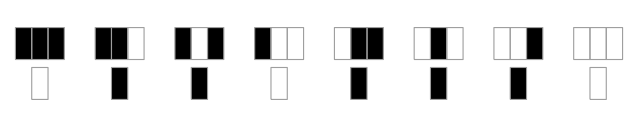

```mathematica
RulePlot[CellularAutomaton[{110,2,1}]]
```

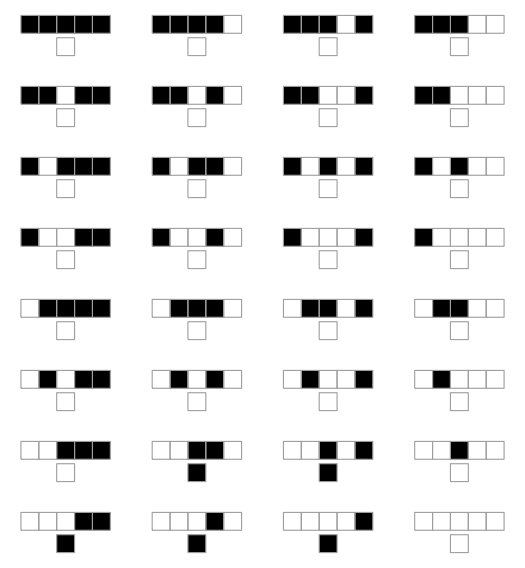

```mathematica
RulePlot[CellularAutomaton[{110,2,2}]]
```

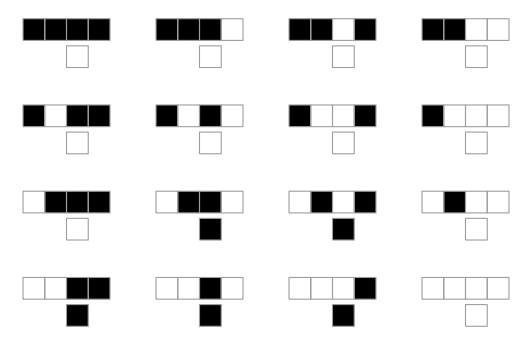

```mathematica
RulePlot[CellularAutomaton[{110,2,3/2}]]
```

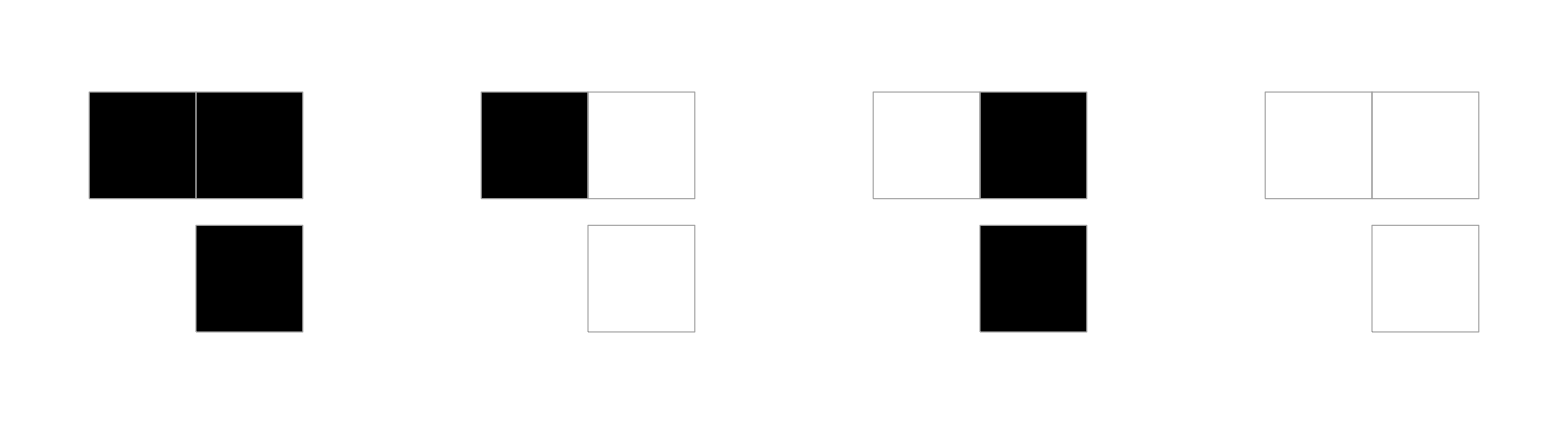

```mathematica
RulePlot[CellularAutomaton[{10,2,1/2}]]
```

```mathematica
CellularAutomaton[{110,2,1},{{1},0},50]==CellularAutomaton[{110,2,{{-1},{0},{1}}},{{1},0},50]
```

True

```mathematica
CellularAutomaton[{110,2,{{-1},{0},{1}}},{{1},0},50]== CellularAutomaton[{110,2,{{0},{1},{-1}}},{{1},0},50]
```

False

```mathematica
CellularAutomaton[{10,2,1/2},{{1},0},50]==CellularAutomaton[{10,2,{{-1},{0}}},{{1},0},50]==CellularAutomaton[{10,2,FlexRadius[0.5]},{{1},0},50]
```

True

## More or less informal representations/descriptions

### Question 1: How can the dynamically equivalent ECA rules 170 and 240 can be described?

```mathematica
DynamicalEquivalenceClass[170]
```

{170,240}

```mathematica
MatrixForm/@{RuleTable[170],RuleTable[240]}
```

{({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 0
{0,0,1} | 1
{0,0,0} | 0),({1,1,1} | 1
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 1
{0,1,1} | 0
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 0)}

```mathematica
GraphicsRow[ArrayPlot/@Module[{ic=RandomInteger[{0,1},100]},
CellularAutomaton[#,ic,100]&/@{170,240}]]
```

-Graphics-

### Question 2: Is there anything special about the dynamically equivalent classes that have a single ECA rule?

```mathematica
Select[equivalenceECAClasses,(Length[#]==1)&]
%//Length
```

{{23},{51},{77},{105},{150},{178},{204},{232}}

```mathematica
RuleTable[150]//MatrixForm
```

({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 0
{1,0,0} | 1
{0,1,1} | 0
{0,1,0} | 1
{0,0,1} | 1
{0,0,0} | 0)

```mathematica
RuleTable[204] (* Identity of the central cell *)
RuleTable[51]   (* Conjugate of the central cell == NOT *)
RuleTable[232] (* Local majority *)
RuleTable[23]   (* Local minority *)
RuleTable[150] (* Local parity (of 1s) == XOR *)
RuleTable[105] (* Conjugate of local parity == XNOR == Local parity of 0s *)
```

```mathematica
(* Same left-right neighbours ⇒ Conjugate of the left-right neighbours *)
(* Otherwise ⇒ Identity of the central cell *)
RuleTable[77]//MatrixForm
```

({1,1,1} | 0
{1,1,0} | 1
{1,0,1} | 0
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 1
{0,0,1} | 0
{0,0,0} | 1)

```mathematica
(* Same left-right neighbours ⇒ Left-right neighbours *)
(* Otherwise ⇒ Conjugate of the central cell *)
RuleTable[178]//MatrixForm
```

({1,1,1} | 1
{1,1,0} | 0
{1,0,1} | 1
{1,0,0} | 1
{0,1,1} | 0
{0,1,0} | 0
{0,0,1} | 1
{0,0,0} | 0)

### The traffic rule 226, leftward displacement of the cars (or 184, rightward displacement)

```mathematica
BFConservativeQ[184]
BFConservativeQ[226]
```

True

True

### Question 3: Which are the number conserving rules of the elementary space?

```mathematica
Select[Range[0,255],BFConservativeQ]
```

{170,184,204,226,240}

```mathematica
GraphicsRow[ArrayPlot/@Module[{ic=RandomInteger[{0,1},100]},
CellularAutomaton[#,ic,100]&/@{184,226}]]
```

-Graphics-

## Boolean representation of a (one-dimensional) binary rule

### From the NKS book: with Logical operators XOR, AND, OR and NOT, and neighbourhood (p, q, r)

http://www.wolframscience.com/nksonline/page-884

### Using CAMat: DNF (Disjunctive Normal Form) ⇒ Logical operators OR, AND and NOT (disjunction with OR)

Tables of Cellular Automaton Properties Pages 516-521: 
https://content.wolfram.com/uploads/sites/34/2020/07/cellular-automaton-properties.pdf

```mathematica
RuleMinDNF[204,1]
RuleMinDNF[170,1]
RuleMinDNF[240,1]
RuleMinDNF[150,1]
```

x_0

x_1

x_-1

(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)

```mathematica
RuleMinDNF[110,1]
```

((!x)_-1&&x_0)||(x_0&&(!x)_1)||((!x)_0&&x_1)

```mathematica
RuleMinDNF[16,1]
```

x_-1&&(!x)_0&&(!x)_1

```mathematica
RuleMinDNF[{0,1}]
RuleMinDNF[{255,1}]
```

{}

{{_,_,_}}

```mathematica
{#,RuleMinDNF[#,1]}&/@Range[0,255]//Column
```

{0,False}
{1,(!x)_-1&&(!x)_0&&(!x)_1}
{2,(!x)_-1&&(!x)_0&&x_1}
{3,(!x)_-1&&(!x)_0}
{4,(!x)_-1&&x_0&&(!x)_1}
{5,(!x)_-1&&(!x)_1}
{6,((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{7,((!x)_-1&&(!x)_0)||((!x)_-1&&(!x)_1)}
{8,(!x)_-1&&x_0&&x_1}
{9,((!x)_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{10,(!x)_-1&&x_1}
{11,((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)}
{12,(!x)_-1&&x_0}
{13,((!x)_-1&&x_0)||((!x)_-1&&(!x)_1)}
{14,((!x)_-1&&x_0)||((!x)_-1&&x_1)}
{15,(!x)_-1}
{16,x_-1&&(!x)_0&&(!x)_1}
{17,(!x)_0&&(!x)_1}
{18,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{19,((!x)_-1&&(!x)_0)||((!x)_0&&(!x)_1)}
{20,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)}
{21,((!x)_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{22,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{23,((!x)_-1&&(!x)_0)||((!x)_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{24,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&x_1)}
{25,((!x)_-1&&x_0&&x_1)||((!x)_0&&(!x)_1)}
{26,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_1)}
{27,((!x)_-1&&x_1)||((!x)_0&&(!x)_1)}
{28,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0)}
{29,((!x)_-1&&x_0)||((!x)_0&&(!x)_1)}
{30,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0)||((!x)_-1&&x_1)}
{31,(!x)_-1||((!x)_0&&(!x)_1)}
{32,x_-1&&(!x)_0&&x_1}
{33,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{34,(!x)_0&&x_1}
{35,((!x)_-1&&(!x)_0)||((!x)_0&&x_1)}
{36,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0&&(!x)_1)}
{37,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&(!x)_1)}
{38,((!x)_-1&&x_0&&(!x)_1)||((!x)_0&&x_1)}
{39,((!x)_-1&&(!x)_1)||((!x)_0&&x_1)}
{40,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0&&x_1)}
{41,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{42,((!x)_-1&&x_1)||((!x)_0&&x_1)}
{43,((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)||((!x)_0&&x_1)}
{44,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0)}
{45,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0)||((!x)_-1&&(!x)_1)}
{46,((!x)_-1&&x_0)||((!x)_0&&x_1)}
{47,(!x)_-1||((!x)_0&&x_1)}
{48,x_-1&&(!x)_0}
{49,(x_-1&&(!x)_0)||((!x)_0&&(!x)_1)}
{50,(x_-1&&(!x)_0)||((!x)_0&&x_1)}
{51,(!x)_0}
{52,(x_-1&&(!x)_0)||((!x)_-1&&x_0&&(!x)_1)}
{53,(x_-1&&(!x)_0)||((!x)_-1&&(!x)_1)}
{54,(x_-1&&(!x)_0)||((!x)_-1&&x_0&&(!x)_1)||((!x)_0&&x_1)}
{55,((!x)_-1&&(!x)_1)||(!x)_0}
{56,(x_-1&&(!x)_0)||((!x)_-1&&x_0&&x_1)}
{57,(x_-1&&(!x)_0)||((!x)_-1&&x_0&&x_1)||((!x)_0&&(!x)_1)}
{58,(x_-1&&(!x)_0)||((!x)_-1&&x_1)}
{59,((!x)_-1&&x_1)||(!x)_0}
{60,(x_-1&&(!x)_0)||((!x)_-1&&x_0)}
{61,(x_-1&&(!x)_0)||((!x)_-1&&x_0)||((!x)_0&&(!x)_1)}
{62,(x_-1&&(!x)_0)||((!x)_-1&&x_0)||((!x)_0&&x_1)}
{63,(!x)_-1||(!x)_0}
{64,x_-1&&x_0&&(!x)_1}
{65,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{66,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{67,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)}
{68,x_0&&(!x)_1}
{69,((!x)_-1&&(!x)_1)||(x_0&&(!x)_1)}
{70,((!x)_-1&&(!x)_0&&x_1)||(x_0&&(!x)_1)}
{71,((!x)_-1&&(!x)_0)||(x_0&&(!x)_1)}
{72,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&x_0&&x_1)}
{73,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{74,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&x_1)}
{75,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)}
{76,((!x)_-1&&x_0)||(x_0&&(!x)_1)}
{77,((!x)_-1&&x_0)||((!x)_-1&&(!x)_1)||(x_0&&(!x)_1)}
{78,((!x)_-1&&x_1)||(x_0&&(!x)_1)}
{79,(!x)_-1||(x_0&&(!x)_1)}
{80,x_-1&&(!x)_1}
{81,(x_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{82,(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{83,(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0)}
{84,(x_-1&&(!x)_1)||(x_0&&(!x)_1)}
{85,(!x)_1}
{86,(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)||(x_0&&(!x)_1)}
{87,((!x)_-1&&(!x)_0)||(!x)_1}
{88,(x_-1&&(!x)_1)||((!x)_-1&&x_0&&x_1)}
{89,(x_-1&&(!x)_1)||((!x)_-1&&x_0&&x_1)||((!x)_0&&(!x)_1)}
{90,(x_-1&&(!x)_1)||((!x)_-1&&x_1)}
{91,(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)}
{92,(x_-1&&(!x)_1)||((!x)_-1&&x_0)}
{93,((!x)_-1&&x_0)||(!x)_1}
{94,(x_-1&&(!x)_1)||((!x)_-1&&x_0)||((!x)_-1&&x_1)}
{95,(!x)_-1||(!x)_1}
{96,(x_-1&&x_0&&(!x)_1)||(x_-1&&(!x)_0&&x_1)}
{97,(x_-1&&x_0&&(!x)_1)||(x_-1&&(!x)_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{98,(x_-1&&x_0&&(!x)_1)||((!x)_0&&x_1)}
{99,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_0&&x_1)}
{100,(x_-1&&(!x)_0&&x_1)||(x_0&&(!x)_1)}
{101,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&(!x)_1)||(x_0&&(!x)_1)}
{102,(x_0&&(!x)_1)||((!x)_0&&x_1)}
{103,((!x)_-1&&(!x)_0)||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{104,(x_-1&&x_0&&(!x)_1)||(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0&&x_1)}
{105,(x_-1&&x_0&&(!x)_1)||(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{106,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&x_1)||((!x)_0&&x_1)}
{107,(x_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)||((!x)_0&&x_1)}
{108,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0)||(x_0&&(!x)_1)}
{109,(x_-1&&(!x)_0&&x_1)||((!x)_-1&&x_0)||((!x)_-1&&(!x)_1)||(x_0&&(!x)_1)}
{110,((!x)_-1&&x_0)||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{111,(!x)_-1||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{112,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)}
{113,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{114,(x_-1&&(!x)_1)||((!x)_0&&x_1)}
{115,(x_-1&&(!x)_1)||(!x)_0}
{116,(x_-1&&(!x)_0)||(x_0&&(!x)_1)}
{117,(x_-1&&(!x)_0)||(!x)_1}
{118,(x_-1&&(!x)_0)||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{119,(!x)_0||(!x)_1}
{120,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)||((!x)_-1&&x_0&&x_1)}
{121,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)||((!x)_-1&&x_0&&x_1)||((!x)_0&&(!x)_1)}
{122,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)||((!x)_-1&&x_1)}
{123,(x_-1&&(!x)_1)||((!x)_-1&&x_1)||(!x)_0}
{124,(x_-1&&(!x)_0)||(x_-1&&(!x)_1)||((!x)_-1&&x_0)}
{125,(x_-1&&(!x)_0)||((!x)_-1&&x_0)||(!x)_1}
{126,(x_-1&&(!x)_1)||((!x)_-1&&x_0)||((!x)_0&&x_1)}
{127,(!x)_-1||(!x)_0||(!x)_1}
{128,x_-1&&x_0&&x_1}
{129,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{130,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0&&x_1)}
{131,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0)}
{132,(x_-1&&x_0&&x_1)||((!x)_-1&&x_0&&(!x)_1)}
{133,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_1)}
{134,(x_-1&&x_0&&x_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{135,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&(!x)_1)}
{136,x_0&&x_1}
{137,((!x)_-1&&(!x)_0&&(!x)_1)||(x_0&&x_1)}
{138,((!x)_-1&&x_1)||(x_0&&x_1)}
{139,((!x)_-1&&(!x)_0)||(x_0&&x_1)}
{140,((!x)_-1&&x_0)||(x_0&&x_1)}
{141,((!x)_-1&&(!x)_1)||(x_0&&x_1)}
{142,((!x)_-1&&x_0)||((!x)_-1&&x_1)||(x_0&&x_1)}
{143,(!x)_-1||(x_0&&x_1)}
{144,(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)}
{145,(x_-1&&x_0&&x_1)||((!x)_0&&(!x)_1)}
{146,(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{147,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0)||((!x)_0&&(!x)_1)}
{148,(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)}
{149,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{150,(x_-1&&x_0&&x_1)||(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{151,(x_-1&&x_0&&x_1)||((!x)_-1&&(!x)_0)||((!x)_-1&&(!x)_1)||((!x)_0&&(!x)_1)}
{152,(x_-1&&(!x)_0&&(!x)_1)||(x_0&&x_1)}
{153,(x_0&&x_1)||((!x)_0&&(!x)_1)}
{154,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_1)||(x_0&&x_1)}
{155,((!x)_-1&&x_1)||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{156,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0)||(x_0&&x_1)}
{157,((!x)_-1&&x_0)||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{158,(x_-1&&(!x)_0&&(!x)_1)||((!x)_-1&&x_0)||((!x)_-1&&x_1)||(x_0&&x_1)}
{159,(!x)_-1||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{160,x_-1&&x_1}
{161,(x_-1&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{162,(x_-1&&x_1)||((!x)_0&&x_1)}
{163,(x_-1&&x_1)||((!x)_-1&&(!x)_0)}
{164,(x_-1&&x_1)||((!x)_-1&&x_0&&(!x)_1)}
{165,(x_-1&&x_1)||((!x)_-1&&(!x)_1)}
{166,(x_-1&&x_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_0&&x_1)}
{167,(x_-1&&x_1)||((!x)_-1&&(!x)_1)||((!x)_0&&x_1)}
{168,(x_-1&&x_1)||(x_0&&x_1)}
{169,(x_-1&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)||(x_0&&x_1)}
{170,x_1}
{171,((!x)_-1&&(!x)_0)||x_1}
{172,(x_-1&&x_1)||((!x)_-1&&x_0)}
{173,(x_-1&&x_1)||((!x)_-1&&(!x)_1)||(x_0&&x_1)}
{174,((!x)_-1&&x_0)||x_1}
{175,(!x)_-1||x_1}
{176,(x_-1&&(!x)_0)||(x_-1&&x_1)}
{177,(x_-1&&x_1)||((!x)_0&&(!x)_1)}
{178,(x_-1&&(!x)_0)||(x_-1&&x_1)||((!x)_0&&x_1)}
{179,(x_-1&&x_1)||(!x)_0}
{180,(x_-1&&(!x)_0)||(x_-1&&x_1)||((!x)_-1&&x_0&&(!x)_1)}
{181,(x_-1&&(!x)_0)||(x_-1&&x_1)||((!x)_-1&&(!x)_1)}
{182,(x_-1&&(!x)_0)||(x_-1&&x_1)||((!x)_-1&&x_0&&(!x)_1)||((!x)_0&&x_1)}
{183,(x_-1&&x_1)||((!x)_-1&&(!x)_1)||(!x)_0}
{184,(x_-1&&(!x)_0)||(x_0&&x_1)}
{185,(x_-1&&x_1)||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{186,(x_-1&&(!x)_0)||x_1}
{187,(!x)_0||x_1}
{188,(x_-1&&(!x)_0)||((!x)_-1&&x_0)||(x_0&&x_1)}
{189,(x_-1&&x_1)||((!x)_-1&&x_0)||((!x)_0&&(!x)_1)}
{190,(x_-1&&(!x)_0)||((!x)_-1&&x_0)||x_1}
{191,(!x)_-1||(!x)_0||x_1}
{192,x_-1&&x_0}
{193,(x_-1&&x_0)||((!x)_-1&&(!x)_0&&(!x)_1)}
{194,(x_-1&&x_0)||((!x)_-1&&(!x)_0&&x_1)}
{195,(x_-1&&x_0)||((!x)_-1&&(!x)_0)}
{196,(x_-1&&x_0)||(x_0&&(!x)_1)}
{197,(x_-1&&x_0)||((!x)_-1&&(!x)_1)}
{198,(x_-1&&x_0)||((!x)_-1&&(!x)_0&&x_1)||(x_0&&(!x)_1)}
{199,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||((!x)_-1&&(!x)_1)}
{200,(x_-1&&x_0)||(x_0&&x_1)}
{201,(x_-1&&x_0)||((!x)_-1&&(!x)_0&&(!x)_1)||(x_0&&x_1)}
{202,(x_-1&&x_0)||((!x)_-1&&x_1)}
{203,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||((!x)_-1&&x_1)}
{204,x_0}
{205,((!x)_-1&&(!x)_1)||x_0}
{206,((!x)_-1&&x_1)||x_0}
{207,(!x)_-1||x_0}
{208,(x_-1&&x_0)||(x_-1&&(!x)_1)}
{209,(x_-1&&x_0)||((!x)_0&&(!x)_1)}
{210,(x_-1&&x_0)||(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)}
{211,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||((!x)_0&&(!x)_1)}
{212,(x_-1&&x_0)||(x_-1&&(!x)_1)||(x_0&&(!x)_1)}
{213,(x_-1&&x_0)||(!x)_1}
{214,(x_-1&&x_0)||(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0&&x_1)||(x_0&&(!x)_1)}
{215,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||(!x)_1}
{216,(x_-1&&(!x)_1)||(x_0&&x_1)}
{217,(x_-1&&x_0)||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{218,(x_-1&&x_0)||(x_-1&&(!x)_1)||((!x)_-1&&x_1)}
{219,(x_-1&&(!x)_1)||((!x)_-1&&(!x)_0)||(x_0&&x_1)}
{220,(x_-1&&(!x)_1)||x_0}
{221,x_0||(!x)_1}
{222,(x_-1&&(!x)_1)||((!x)_-1&&x_1)||x_0}
{223,(!x)_-1||x_0||(!x)_1}
{224,(x_-1&&x_0)||(x_-1&&x_1)}
{225,(x_-1&&x_0)||(x_-1&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)}
{226,(x_-1&&x_0)||((!x)_0&&x_1)}
{227,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||((!x)_0&&x_1)}
{228,(x_-1&&x_1)||(x_0&&(!x)_1)}
{229,(x_-1&&x_0)||(x_-1&&x_1)||((!x)_-1&&(!x)_1)}
{230,(x_-1&&x_0)||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{231,(x_-1&&x_1)||((!x)_-1&&(!x)_0)||(x_0&&(!x)_1)}
{232,(x_-1&&x_0)||(x_-1&&x_1)||(x_0&&x_1)}
{233,(x_-1&&x_0)||(x_-1&&x_1)||((!x)_-1&&(!x)_0&&(!x)_1)||(x_0&&x_1)}
{234,(x_-1&&x_0)||x_1}
{235,(x_-1&&x_0)||((!x)_-1&&(!x)_0)||x_1}
{236,(x_-1&&x_1)||x_0}
{237,(x_-1&&x_1)||((!x)_-1&&(!x)_1)||x_0}
{238,x_0||x_1}
{239,(!x)_-1||x_0||x_1}
{240,x_-1}
{241,x_-1||((!x)_0&&(!x)_1)}
{242,x_-1||((!x)_0&&x_1)}
{243,x_-1||(!x)_0}
{244,x_-1||(x_0&&(!x)_1)}
{245,x_-1||(!x)_1}
{246,x_-1||(x_0&&(!x)_1)||((!x)_0&&x_1)}
{247,x_-1||(!x)_0||(!x)_1}
{248,x_-1||(x_0&&x_1)}
{249,x_-1||(x_0&&x_1)||((!x)_0&&(!x)_1)}
{250,x_-1||x_1}
{251,x_-1||(!x)_0||x_1}
{252,x_-1||x_0}
{253,x_-1||x_0||(!x)_1}
{254,x_-1||x_0||x_1}
{255,True}

### Using CAMat: DNF with bits and don’t-cares (with choice of the reference bit)

```mathematica
RuleMinDNF[232,1]
RuleMinDNF[{232,1},1]
RuleMinDNF[{232,1},0]
```

(x_-1&&x_0)||(x_-1&&x_1)||(x_0&&x_1)

{{1,1,_},{1,_,1},{_,1,1}}

{{0,0,_},{0,_,0},{_,0,0}}

```mathematica
RuleMinDNF[0,1]
RuleMinDNF[255,1]
```

False

True

```mathematica
RuleTable[232]//MatrixForm
```

({1,1,1} | 1
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 0
{0,0,1} | 0
{0,0,0} | 0)

```mathematica
{#,RuleMinDNF[{#,1}]}&/@Range[0,255]//Column
```

{0,{}}
{1,{{0,0,0}}}
{2,{{0,0,1}}}
{3,{{0,0,_}}}
{4,{{0,1,0}}}
{5,{{0,_,0}}}
{6,{{0,1,0},{0,0,1}}}
{7,{{0,0,_},{0,_,0}}}
{8,{{0,1,1}}}
{9,{{0,1,1},{0,0,0}}}
{10,{{0,_,1}}}
{11,{{0,0,_},{0,_,1}}}
{12,{{0,1,_}}}
{13,{{0,1,_},{0,_,0}}}
{14,{{0,1,_},{0,_,1}}}
{15,{{0,_,_}}}
{16,{{1,0,0}}}
{17,{{_,0,0}}}
{18,{{1,0,0},{0,0,1}}}
{19,{{0,0,_},{_,0,0}}}
{20,{{1,0,0},{0,1,0}}}
{21,{{0,_,0},{_,0,0}}}
{22,{{1,0,0},{0,1,0},{0,0,1}}}
{23,{{0,0,_},{0,_,0},{_,0,0}}}
{24,{{1,0,0},{0,1,1}}}
{25,{{0,1,1},{_,0,0}}}
{26,{{1,0,0},{0,_,1}}}
{27,{{0,_,1},{_,0,0}}}
{28,{{1,0,0},{0,1,_}}}
{29,{{0,1,_},{_,0,0}}}
{30,{{1,0,0},{0,1,_},{0,_,1}}}
{31,{{0,_,_},{_,0,0}}}
{32,{{1,0,1}}}
{33,{{1,0,1},{0,0,0}}}
{34,{{_,0,1}}}
{35,{{0,0,_},{_,0,1}}}
{36,{{1,0,1},{0,1,0}}}
{37,{{1,0,1},{0,_,0}}}
{38,{{0,1,0},{_,0,1}}}
{39,{{0,_,0},{_,0,1}}}
{40,{{1,0,1},{0,1,1}}}
{41,{{1,0,1},{0,1,1},{0,0,0}}}
{42,{{0,_,1},{_,0,1}}}
{43,{{0,0,_},{0,_,1},{_,0,1}}}
{44,{{1,0,1},{0,1,_}}}
{45,{{1,0,1},{0,1,_},{0,_,0}}}
{46,{{0,1,_},{_,0,1}}}
{47,{{0,_,_},{_,0,1}}}
{48,{{1,0,_}}}
{49,{{1,0,_},{_,0,0}}}
{50,{{1,0,_},{_,0,1}}}
{51,{{_,0,_}}}
{52,{{1,0,_},{0,1,0}}}
{53,{{1,0,_},{0,_,0}}}
{54,{{1,0,_},{0,1,0},{_,0,1}}}
{55,{{0,_,0},{_,0,_}}}
{56,{{1,0,_},{0,1,1}}}
{57,{{1,0,_},{0,1,1},{_,0,0}}}
{58,{{1,0,_},{0,_,1}}}
{59,{{0,_,1},{_,0,_}}}
{60,{{1,0,_},{0,1,_}}}
{61,{{1,0,_},{0,1,_},{_,0,0}}}
{62,{{1,0,_},{0,1,_},{_,0,1}}}
{63,{{0,_,_},{_,0,_}}}
{64,{{1,1,0}}}
{65,{{1,1,0},{0,0,0}}}
{66,{{1,1,0},{0,0,1}}}
{67,{{1,1,0},{0,0,_}}}
{68,{{_,1,0}}}
{69,{{0,_,0},{_,1,0}}}
{70,{{0,0,1},{_,1,0}}}
{71,{{0,0,_},{_,1,0}}}
{72,{{1,1,0},{0,1,1}}}
{73,{{1,1,0},{0,1,1},{0,0,0}}}
{74,{{1,1,0},{0,_,1}}}
{75,{{1,1,0},{0,0,_},{0,_,1}}}
{76,{{0,1,_},{_,1,0}}}
{77,{{0,1,_},{0,_,0},{_,1,0}}}
{78,{{0,_,1},{_,1,0}}}
{79,{{0,_,_},{_,1,0}}}
{80,{{1,_,0}}}
{81,{{1,_,0},{_,0,0}}}
{82,{{1,_,0},{0,0,1}}}
{83,{{1,_,0},{0,0,_}}}
{84,{{1,_,0},{_,1,0}}}
{85,{{_,_,0}}}
{86,{{1,_,0},{0,0,1},{_,1,0}}}
{87,{{0,0,_},{_,_,0}}}
{88,{{1,_,0},{0,1,1}}}
{89,{{1,_,0},{0,1,1},{_,0,0}}}
{90,{{1,_,0},{0,_,1}}}
{91,{{1,_,0},{0,0,_},{0,_,1}}}
{92,{{1,_,0},{0,1,_}}}
{93,{{0,1,_},{_,_,0}}}
{94,{{1,_,0},{0,1,_},{0,_,1}}}
{95,{{0,_,_},{_,_,0}}}
{96,{{1,1,0},{1,0,1}}}
{97,{{1,1,0},{1,0,1},{0,0,0}}}
{98,{{1,1,0},{_,0,1}}}
{99,{{1,1,0},{0,0,_},{_,0,1}}}
{100,{{1,0,1},{_,1,0}}}
{101,{{1,0,1},{0,_,0},{_,1,0}}}
{102,{{_,1,0},{_,0,1}}}
{103,{{0,0,_},{_,1,0},{_,0,1}}}
{104,{{1,1,0},{1,0,1},{0,1,1}}}
{105,{{1,1,0},{1,0,1},{0,1,1},{0,0,0}}}
{106,{{1,1,0},{0,_,1},{_,0,1}}}
{107,{{1,1,0},{0,0,_},{0,_,1},{_,0,1}}}
{108,{{1,0,1},{0,1,_},{_,1,0}}}
{109,{{1,0,1},{0,1,_},{0,_,0},{_,1,0}}}
{110,{{0,1,_},{_,1,0},{_,0,1}}}
{111,{{0,_,_},{_,1,0},{_,0,1}}}
{112,{{1,0,_},{1,_,0}}}
{113,{{1,0,_},{1,_,0},{_,0,0}}}
{114,{{1,_,0},{_,0,1}}}
{115,{{1,_,0},{_,0,_}}}
{116,{{1,0,_},{_,1,0}}}
{117,{{1,0,_},{_,_,0}}}
{118,{{1,0,_},{_,1,0},{_,0,1}}}
{119,{{_,0,_},{_,_,0}}}
{120,{{1,0,_},{1,_,0},{0,1,1}}}
{121,{{1,0,_},{1,_,0},{0,1,1},{_,0,0}}}
{122,{{1,0,_},{1,_,0},{0,_,1}}}
{123,{{1,_,0},{0,_,1},{_,0,_}}}
{124,{{1,0,_},{1,_,0},{0,1,_}}}
{125,{{1,0,_},{0,1,_},{_,_,0}}}
{126,{{1,_,0},{0,1,_},{_,0,1}}}
{127,{{0,_,_},{_,0,_},{_,_,0}}}
{128,{{1,1,1}}}
{129,{{1,1,1},{0,0,0}}}
{130,{{1,1,1},{0,0,1}}}
{131,{{1,1,1},{0,0,_}}}
{132,{{1,1,1},{0,1,0}}}
{133,{{1,1,1},{0,_,0}}}
{134,{{1,1,1},{0,1,0},{0,0,1}}}
{135,{{1,1,1},{0,0,_},{0,_,0}}}
{136,{{_,1,1}}}
{137,{{0,0,0},{_,1,1}}}
{138,{{0,_,1},{_,1,1}}}
{139,{{0,0,_},{_,1,1}}}
{140,{{0,1,_},{_,1,1}}}
{141,{{0,_,0},{_,1,1}}}
{142,{{0,1,_},{0,_,1},{_,1,1}}}
{143,{{0,_,_},{_,1,1}}}
{144,{{1,1,1},{1,0,0}}}
{145,{{1,1,1},{_,0,0}}}
{146,{{1,1,1},{1,0,0},{0,0,1}}}
{147,{{1,1,1},{0,0,_},{_,0,0}}}
{148,{{1,1,1},{1,0,0},{0,1,0}}}
{149,{{1,1,1},{0,_,0},{_,0,0}}}
{150,{{1,1,1},{1,0,0},{0,1,0},{0,0,1}}}
{151,{{1,1,1},{0,0,_},{0,_,0},{_,0,0}}}
{152,{{1,0,0},{_,1,1}}}
{153,{{_,1,1},{_,0,0}}}
{154,{{1,0,0},{0,_,1},{_,1,1}}}
{155,{{0,_,1},{_,1,1},{_,0,0}}}
{156,{{1,0,0},{0,1,_},{_,1,1}}}
{157,{{0,1,_},{_,1,1},{_,0,0}}}
{158,{{1,0,0},{0,1,_},{0,_,1},{_,1,1}}}
{159,{{0,_,_},{_,1,1},{_,0,0}}}
{160,{{1,_,1}}}
{161,{{1,_,1},{0,0,0}}}
{162,{{1,_,1},{_,0,1}}}
{163,{{1,_,1},{0,0,_}}}
{164,{{1,_,1},{0,1,0}}}
{165,{{1,_,1},{0,_,0}}}
{166,{{1,_,1},{0,1,0},{_,0,1}}}
{167,{{1,_,1},{0,_,0},{_,0,1}}}
{168,{{1,_,1},{_,1,1}}}
{169,{{1,_,1},{0,0,0},{_,1,1}}}
{170,{{_,_,1}}}
{171,{{0,0,_},{_,_,1}}}
{172,{{1,_,1},{0,1,_}}}
{173,{{1,_,1},{0,_,0},{_,1,1}}}
{174,{{0,1,_},{_,_,1}}}
{175,{{0,_,_},{_,_,1}}}
{176,{{1,0,_},{1,_,1}}}
{177,{{1,_,1},{_,0,0}}}
{178,{{1,0,_},{1,_,1},{_,0,1}}}
{179,{{1,_,1},{_,0,_}}}
{180,{{1,0,_},{1,_,1},{0,1,0}}}
{181,{{1,0,_},{1,_,1},{0,_,0}}}
{182,{{1,0,_},{1,_,1},{0,1,0},{_,0,1}}}
{183,{{1,_,1},{0,_,0},{_,0,_}}}
{184,{{1,0,_},{_,1,1}}}
{185,{{1,_,1},{_,1,1},{_,0,0}}}
{186,{{1,0,_},{_,_,1}}}
{187,{{_,0,_},{_,_,1}}}
{188,{{1,0,_},{0,1,_},{_,1,1}}}
{189,{{1,_,1},{0,1,_},{_,0,0}}}
{190,{{1,0,_},{0,1,_},{_,_,1}}}
{191,{{0,_,_},{_,0,_},{_,_,1}}}
{192,{{1,1,_}}}
{193,{{1,1,_},{0,0,0}}}
{194,{{1,1,_},{0,0,1}}}
{195,{{1,1,_},{0,0,_}}}
{196,{{1,1,_},{_,1,0}}}
{197,{{1,1,_},{0,_,0}}}
{198,{{1,1,_},{0,0,1},{_,1,0}}}
{199,{{1,1,_},{0,0,_},{0,_,0}}}
{200,{{1,1,_},{_,1,1}}}
{201,{{1,1,_},{0,0,0},{_,1,1}}}
{202,{{1,1,_},{0,_,1}}}
{203,{{1,1,_},{0,0,_},{0,_,1}}}
{204,{{_,1,_}}}
{205,{{0,_,0},{_,1,_}}}
{206,{{0,_,1},{_,1,_}}}
{207,{{0,_,_},{_,1,_}}}
{208,{{1,1,_},{1,_,0}}}
{209,{{1,1,_},{_,0,0}}}
{210,{{1,1,_},{1,_,0},{0,0,1}}}
{211,{{1,1,_},{0,0,_},{_,0,0}}}
{212,{{1,1,_},{1,_,0},{_,1,0}}}
{213,{{1,1,_},{_,_,0}}}
{214,{{1,1,_},{1,_,0},{0,0,1},{_,1,0}}}
{215,{{1,1,_},{0,0,_},{_,_,0}}}
{216,{{1,_,0},{_,1,1}}}
{217,{{1,1,_},{_,1,1},{_,0,0}}}
{218,{{1,1,_},{1,_,0},{0,_,1}}}
{219,{{1,_,0},{0,0,_},{_,1,1}}}
{220,{{1,_,0},{_,1,_}}}
{221,{{_,1,_},{_,_,0}}}
{222,{{1,_,0},{0,_,1},{_,1,_}}}
{223,{{0,_,_},{_,1,_},{_,_,0}}}
{224,{{1,1,_},{1,_,1}}}
{225,{{1,1,_},{1,_,1},{0,0,0}}}
{226,{{1,1,_},{_,0,1}}}
{227,{{1,1,_},{0,0,_},{_,0,1}}}
{228,{{1,_,1},{_,1,0}}}
{229,{{1,1,_},{1,_,1},{0,_,0}}}
{230,{{1,1,_},{_,1,0},{_,0,1}}}
{231,{{1,_,1},{0,0,_},{_,1,0}}}
{232,{{1,1,_},{1,_,1},{_,1,1}}}
{233,{{1,1,_},{1,_,1},{0,0,0},{_,1,1}}}
{234,{{1,1,_},{_,_,1}}}
{235,{{1,1,_},{0,0,_},{_,_,1}}}
{236,{{1,_,1},{_,1,_}}}
{237,{{1,_,1},{0,_,0},{_,1,_}}}
{238,{{_,1,_},{_,_,1}}}
{239,{{0,_,_},{_,1,_},{_,_,1}}}
{240,{{1,_,_}}}
{241,{{1,_,_},{_,0,0}}}
{242,{{1,_,_},{_,0,1}}}
{243,{{1,_,_},{_,0,_}}}
{244,{{1,_,_},{_,1,0}}}
{245,{{1,_,_},{_,_,0}}}
{246,{{1,_,_},{_,1,0},{_,0,1}}}
{247,{{1,_,_},{_,0,_},{_,_,0}}}
{248,{{1,_,_},{_,1,1}}}
{249,{{1,_,_},{_,1,1},{_,0,0}}}
{250,{{1,_,_},{_,_,1}}}
{251,{{1,_,_},{_,0,_},{_,_,1}}}
{252,{{1,_,_},{_,1,_}}}
{253,{{1,_,_},{_,1,_},{_,_,0}}}
{254,{{1,_,_},{_,1,_},{_,_,1}}}
{255,{{_,_,_}}}

### Using CAMat: ANF (Algebraic Normal Form) ⇒ Logical operators XOR, AND and NOT (disjunction with XOR)

```mathematica
RuleMinDNF[16,1]
RuleMinANF[16,1]
```

x_-1&&(!x)_0&&(!x)_1

(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1

```mathematica
{#,RuleMinANF[#,1]}&/@Range[0,255]//Column
```

{0,False}
{1,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{2,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{3,!((x_-1&&x_0)⊻x_-1⊻x_0)}
{4,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{5,!((x_-1&&x_1)⊻x_-1⊻x_1)}
{6,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_0⊻x_1}
{7,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{8,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)}
{9,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_0⊻x_1)}
{10,(x_-1&&x_1)⊻x_1}
{11,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{12,(x_-1&&x_0)⊻x_0}
{13,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{14,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{15,!x_-1}
{16,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{17,!((x_0&&x_1)⊻x_0⊻x_1)}
{18,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_1}
{19,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{20,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0}
{21,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{22,(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{23,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1))}
{24,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1}
{25,!((x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{26,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{27,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_0)}
{28,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{29,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_1)}
{30,(x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{31,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1))}
{32,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)}
{33,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{34,(x_0&&x_1)⊻x_1}
{35,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{36,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0}
{37,!((x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{38,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{39,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1)}
{40,(x_-1&&x_1)⊻(x_0&&x_1)}
{41,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{42,(x_-1&&x_0&&x_1)⊻x_1}
{43,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0)}
{44,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{45,!((x_0&&x_1)⊻x_-1⊻x_1)}
{46,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_0⊻x_1}
{47,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{48,(x_-1&&x_0)⊻x_-1}
{49,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{50,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{51,!x_0}
{52,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{53,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_1)}
{54,(x_-1&&x_1)⊻x_-1⊻x_0⊻x_1}
{55,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1))}
{56,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{57,!((x_-1&&x_1)⊻x_0⊻x_1)}
{58,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_1}
{59,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{60,x_-1⊻x_0}
{61,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{62,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{63,!(x_-1&&x_0)}
{64,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)}
{65,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{66,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_1}
{67,!((x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{68,(x_0&&x_1)⊻x_0}
{69,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{70,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{71,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1)}
{72,(x_-1&&x_0)⊻(x_0&&x_1)}
{73,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{74,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{75,!((x_0&&x_1)⊻x_-1⊻x_0)}
{76,(x_-1&&x_0&&x_1)⊻x_0}
{77,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_1)}
{78,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0⊻x_1}
{79,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{80,(x_-1&&x_1)⊻x_-1}
{81,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{82,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{83,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_0)}
{84,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{85,!x_1}
{86,(x_-1&&x_0)⊻x_-1⊻x_0⊻x_1}
{87,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1))}
{88,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{89,!((x_-1&&x_0)⊻x_0⊻x_1)}
{90,x_-1⊻x_1}
{91,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{92,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_0}
{93,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{94,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{95,!(x_-1&&x_1)}
{96,(x_-1&&x_0)⊻(x_-1&&x_1)}
{97,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{98,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{99,!((x_-1&&x_1)⊻x_-1⊻x_0)}
{100,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{101,!((x_-1&&x_0)⊻x_-1⊻x_1)}
{102,x_0⊻x_1}
{103,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{104,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)}
{105,!(x_-1⊻x_0⊻x_1)}
{106,(x_-1&&x_0)⊻x_1}
{107,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{108,(x_-1&&x_1)⊻x_0}
{109,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{110,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{111,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1)}
{112,(x_-1&&x_0&&x_1)⊻x_-1}
{113,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0⊻x_1)}
{114,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_1}
{115,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{116,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_0}
{117,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{118,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{119,!(x_0&&x_1)}
{120,(x_0&&x_1)⊻x_-1}
{121,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{122,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{123,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_0)}
{124,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{125,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_1)}
{126,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{127,!(x_-1&&x_0&&x_1)}
{128,x_-1&&x_0&&x_1}
{129,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{130,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_1}
{131,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{132,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_0}
{133,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{134,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{135,!((x_0&&x_1)⊻x_-1)}
{136,x_0&&x_1}
{137,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{138,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{139,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_0)}
{140,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_0}
{141,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_1)}
{142,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0⊻x_1}
{143,!((x_-1&&x_0&&x_1)⊻x_-1)}
{144,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1}
{145,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{146,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{147,!((x_-1&&x_1)⊻x_0)}
{148,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{149,!((x_-1&&x_0)⊻x_1)}
{150,x_-1⊻x_0⊻x_1}
{151,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1))}
{152,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{153,!(x_0⊻x_1)}
{154,(x_-1&&x_0)⊻x_-1⊻x_1}
{155,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{156,(x_-1&&x_1)⊻x_-1⊻x_0}
{157,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{158,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{159,!((x_-1&&x_0)⊻(x_-1&&x_1))}
{160,x_-1&&x_1}
{161,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{162,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{163,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_0)}
{164,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{165,!(x_-1⊻x_1)}
{166,(x_-1&&x_0)⊻x_0⊻x_1}
{167,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{168,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)}
{169,!((x_-1&&x_0)⊻x_-1⊻x_0⊻x_1)}
{170,x_1}
{171,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{172,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_0}
{173,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{174,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{175,!((x_-1&&x_1)⊻x_-1)}
{176,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{177,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_0⊻x_1)}
{178,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_1}
{179,!((x_-1&&x_0&&x_1)⊻x_0)}
{180,(x_0&&x_1)⊻x_-1⊻x_0}
{181,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{182,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{183,!((x_-1&&x_0)⊻(x_0&&x_1))}
{184,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1}
{185,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{186,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{187,!((x_0&&x_1)⊻x_0)}
{188,(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{189,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_1)}
{190,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{191,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1))}
{192,x_-1&&x_0}
{193,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{194,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1}
{195,!(x_-1⊻x_0)}
{196,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{197,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_1)}
{198,(x_-1&&x_1)⊻x_0⊻x_1}
{199,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{200,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)}
{201,!((x_-1&&x_1)⊻x_-1⊻x_0⊻x_1)}
{202,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_1}
{203,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{204,x_0}
{205,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{206,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{207,!((x_-1&&x_0)⊻x_-1)}
{208,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{209,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_0⊻x_1)}
{210,(x_0&&x_1)⊻x_-1⊻x_1}
{211,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{212,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0}
{213,!((x_-1&&x_0&&x_1)⊻x_1)}
{214,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{215,!((x_-1&&x_1)⊻(x_0&&x_1))}
{216,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1}
{217,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{218,(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{219,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0)}
{220,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{221,!((x_0&&x_1)⊻x_1)}
{222,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{223,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1))}
{224,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)}
{225,!((x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{226,(x_-1&&x_0)⊻(x_0&&x_1)⊻x_1}
{227,!((x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0)}
{228,(x_-1&&x_1)⊻(x_0&&x_1)⊻x_0}
{229,!((x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1)}
{230,(x_-1&&x_0&&x_1)⊻x_0⊻x_1}
{231,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1)}
{232,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)}
{233,!((x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1)}
{234,(x_-1&&x_0)⊻(x_-1&&x_0&&x_1)⊻x_1}
{235,!((x_-1&&x_1)⊻(x_0&&x_1)⊻x_-1⊻x_0)}
{236,(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0}
{237,!((x_-1&&x_0)⊻(x_0&&x_1)⊻x_-1⊻x_1)}
{238,(x_0&&x_1)⊻x_0⊻x_1}
{239,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1)}
{240,x_-1}
{241,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0⊻x_1)}
{242,(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_1}
{243,!((x_-1&&x_0)⊻x_0)}
{244,(x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0}
{245,!((x_-1&&x_1)⊻x_1)}
{246,(x_-1&&x_0)⊻(x_-1&&x_1)⊻x_-1⊻x_0⊻x_1}
{247,!((x_0&&x_1)⊻(x_-1&&x_0&&x_1))}
{248,(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1}
{249,!((x_-1&&x_0)⊻(x_-1&&x_1)⊻x_0⊻x_1)}
{250,(x_-1&&x_1)⊻x_-1⊻x_1}
{251,!((x_-1&&x_0)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_0)}
{252,(x_-1&&x_0)⊻x_-1⊻x_0}
{253,!((x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_1)}
{254,(x_-1&&x_0)⊻(x_-1&&x_1)⊻(x_0&&x_1)⊻(x_-1&&x_0&&x_1)⊻x_-1⊻x_0⊻x_1}
{255,True}

### Question 4: ECA rules 15 and 85 are number conserving at every other time step. How can this behaviour be explained? To be convinced, run them.

### Question 5: ECA rule 71 also seems to have the same behaviour as before. Is it really so?

## Algebraic representation

### From the NKS Atlas: All ECA rules in algebraic form (p, q, r) → {0, 1}

http://atlas.wolfram.com/01/01/views/173/TableView.html

### Using CAMaT

```mathematica
AlgebraicRepresentation[40,1,ANF]
```

(x_-1+x_0) x_1

```mathematica
AlgebraicRepresentation[150,1,DNF]
AlgebraicRepresentation[150,1,ANF]
```

Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]

x_-1+x_0+x_1

```mathematica
AlgebraicRepresentation[0,1,DNF]
AlgebraicRepresentation[0,1,ANF]
AlgebraicRepresentation[255,1,DNF]
AlgebraicRepresentation[255,1,ANF]
```

False

False

True

True

```mathematica
{#,AlgebraicRepresentation[#,1,DNF]}&/@Range[0,255]//Column
```

{0,Mod[False,2]}
{1,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1),2]}
{2,Mod[((1-x)_-1) ((1-x)_0) x_1,2]}
{3,Mod[((1-x)_-1) ((1-x)_0),2]}
{4,Mod[((1-x)_-1) ((1-x)_1) x_0,2]}
{5,Mod[((1-x)_-1) ((1-x)_1),2]}
{6,Mod[((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{7,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) ((1-x)_1),2]}
{8,Mod[((1-x)_-1) x_0 x_1,2]}
{9,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_-1) x_0 x_1,2]}
{10,Mod[((1-x)_-1) x_1,2]}
{11,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) x_1,2]}
{12,Mod[((1-x)_-1) x_0,2]}
{13,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_-1) x_0,2]}
{14,Mod[((1-x)_-1) x_0+((1-x)_-1) x_1,2]}
{15,Mod[(1-x)_-1,2]}
{16,Mod[((1-x)_0) ((1-x)_1) x_-1,2]}
{17,Mod[((1-x)_0) ((1-x)_1),2]}
{18,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_0) x_1,2]}
{19,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_0) ((1-x)_1),2]}
{20,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0,2]}
{21,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) ((1-x)_1),2]}
{22,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{23,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) ((1-x)_1)+((1-x)_0) ((1-x)_1),2]}
{24,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_0 x_1,2]}
{25,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_0 x_1,2]}
{26,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_1,2]}
{27,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_1,2]}
{28,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_0,2]}
{29,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_0,2]}
{30,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_0+((1-x)_-1) x_1,2]}
{31,Mod[((1-x)_-1)+((1-x)_0) ((1-x)_1),2]}
{32,Mod[((1-x)_0) x_-1 x_1,2]}
{33,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1 x_1,2]}
{34,Mod[((1-x)_0) x_1,2]}
{35,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_0) x_1,2]}
{36,Mod[((1-x)_-1) ((1-x)_1) x_0+((1-x)_0) x_-1 x_1,2]}
{37,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) x_-1 x_1,2]}
{38,Mod[((1-x)_-1) ((1-x)_1) x_0+((1-x)_0) x_1,2]}
{39,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) x_1,2]}
{40,Mod[((1-x)_0) x_-1 x_1+((1-x)_-1) x_0 x_1,2]}
{41,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1 x_1+((1-x)_-1) x_0 x_1,2]}
{42,Mod[((1-x)_-1) x_1+((1-x)_0) x_1,2]}
{43,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) x_1+((1-x)_0) x_1,2]}
{44,Mod[((1-x)_-1) x_0+((1-x)_0) x_-1 x_1,2]}
{45,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_-1) x_0+((1-x)_0) x_-1 x_1,2]}
{46,Mod[((1-x)_-1) x_0+((1-x)_0) x_1,2]}
{47,Mod[((1-x)_-1)+((1-x)_0) x_1,2]}
{48,Mod[((1-x)_0) x_-1,2]}
{49,Mod[((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1,2]}
{50,Mod[((1-x)_0) x_-1+((1-x)_0) x_1,2]}
{51,Mod[(1-x)_0,2]}
{52,Mod[((1-x)_0) x_-1+((1-x)_-1) ((1-x)_1) x_0,2]}
{53,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) x_-1,2]}
{54,Mod[((1-x)_0) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_0) x_1,2]}
{55,Mod[((1-x)_0)+((1-x)_-1) ((1-x)_1),2]}
{56,Mod[((1-x)_0) x_-1+((1-x)_-1) x_0 x_1,2]}
{57,Mod[((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1+((1-x)_-1) x_0 x_1,2]}
{58,Mod[((1-x)_0) x_-1+((1-x)_-1) x_1,2]}
{59,Mod[((1-x)_0)+((1-x)_-1) x_1,2]}
{60,Mod[((1-x)_0) x_-1+((1-x)_-1) x_0,2]}
{61,Mod[((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1+((1-x)_-1) x_0,2]}
{62,Mod[((1-x)_0) x_-1+((1-x)_-1) x_0+((1-x)_0) x_1,2]}
{63,Mod[((1-x)_-1)+((1-x)_0),2]}
{64,Mod[((1-x)_1) x_-1 x_0,2]}
{65,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1 x_0,2]}
{66,Mod[((1-x)_1) x_-1 x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{67,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1 x_0,2]}
{68,Mod[((1-x)_1) x_0,2]}
{69,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_1) x_0,2]}
{70,Mod[((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{71,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_0,2]}
{72,Mod[((1-x)_1) x_-1 x_0+((1-x)_-1) x_0 x_1,2]}
{73,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1 x_0+((1-x)_-1) x_0 x_1,2]}
{74,Mod[((1-x)_1) x_-1 x_0+((1-x)_-1) x_1,2]}
{75,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1 x_0+((1-x)_-1) x_1,2]}
{76,Mod[((1-x)_-1) x_0+((1-x)_1) x_0,2]}
{77,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_-1) x_0+((1-x)_1) x_0,2]}
{78,Mod[((1-x)_1) x_0+((1-x)_-1) x_1,2]}
{79,Mod[((1-x)_-1)+((1-x)_1) x_0,2]}
{80,Mod[((1-x)_1) x_-1,2]}
{81,Mod[((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1,2]}
{82,Mod[((1-x)_1) x_-1+((1-x)_-1) ((1-x)_0) x_1,2]}
{83,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1,2]}
{84,Mod[((1-x)_1) x_-1+((1-x)_1) x_0,2]}
{85,Mod[(1-x)_1,2]}
{86,Mod[((1-x)_1) x_-1+((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{87,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1),2]}
{88,Mod[((1-x)_1) x_-1+((1-x)_-1) x_0 x_1,2]}
{89,Mod[((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1+((1-x)_-1) x_0 x_1,2]}
{90,Mod[((1-x)_1) x_-1+((1-x)_-1) x_1,2]}
{91,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1+((1-x)_-1) x_1,2]}
{92,Mod[((1-x)_1) x_-1+((1-x)_-1) x_0,2]}
{93,Mod[((1-x)_1)+((1-x)_-1) x_0,2]}
{94,Mod[((1-x)_1) x_-1+((1-x)_-1) x_0+((1-x)_-1) x_1,2]}
{95,Mod[((1-x)_-1)+((1-x)_1),2]}
{96,Mod[((1-x)_1) x_-1 x_0+((1-x)_0) x_-1 x_1,2]}
{97,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1 x_0+((1-x)_0) x_-1 x_1,2]}
{98,Mod[((1-x)_1) x_-1 x_0+((1-x)_0) x_1,2]}
{99,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1 x_0+((1-x)_0) x_1,2]}
{100,Mod[((1-x)_1) x_0+((1-x)_0) x_-1 x_1,2]}
{101,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_1) x_0+((1-x)_0) x_-1 x_1,2]}
{102,Mod[((1-x)_1) x_0+((1-x)_0) x_1,2]}
{103,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_0+((1-x)_0) x_1,2]}
{104,Mod[((1-x)_1) x_-1 x_0+((1-x)_0) x_-1 x_1+((1-x)_-1) x_0 x_1,2]}
{105,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+((1-x)_1) x_-1 x_0+((1-x)_0) x_-1 x_1+((1-x)_-1) x_0 x_1,2]}
{106,Mod[((1-x)_1) x_-1 x_0+((1-x)_-1) x_1+((1-x)_0) x_1,2]}
{107,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1 x_0+((1-x)_-1) x_1+((1-x)_0) x_1,2]}
{108,Mod[((1-x)_-1) x_0+((1-x)_1) x_0+((1-x)_0) x_-1 x_1,2]}
{109,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_-1) x_0+((1-x)_1) x_0+((1-x)_0) x_-1 x_1,2]}
{110,Mod[((1-x)_-1) x_0+((1-x)_1) x_0+((1-x)_0) x_1,2]}
{111,Mod[((1-x)_-1)+((1-x)_1) x_0+((1-x)_0) x_1,2]}
{112,Mod[((1-x)_0) x_-1+((1-x)_1) x_-1,2]}
{113,Mod[((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1+((1-x)_1) x_-1,2]}
{114,Mod[((1-x)_1) x_-1+((1-x)_0) x_1,2]}
{115,Mod[((1-x)_0)+((1-x)_1) x_-1,2]}
{116,Mod[((1-x)_0) x_-1+((1-x)_1) x_0,2]}
{117,Mod[((1-x)_1)+((1-x)_0) x_-1,2]}
{118,Mod[((1-x)_0) x_-1+((1-x)_1) x_0+((1-x)_0) x_1,2]}
{119,Mod[((1-x)_0)+((1-x)_1),2]}
{120,Mod[((1-x)_0) x_-1+((1-x)_1) x_-1+((1-x)_-1) x_0 x_1,2]}
{121,Mod[((1-x)_0) ((1-x)_1)+((1-x)_0) x_-1+((1-x)_1) x_-1+((1-x)_-1) x_0 x_1,2]}
{122,Mod[((1-x)_0) x_-1+((1-x)_1) x_-1+((1-x)_-1) x_1,2]}
{123,Mod[((1-x)_0)+((1-x)_1) x_-1+((1-x)_-1) x_1,2]}
{124,Mod[((1-x)_0) x_-1+((1-x)_1) x_-1+((1-x)_-1) x_0,2]}
{125,Mod[((1-x)_1)+((1-x)_0) x_-1+((1-x)_-1) x_0,2]}
{126,Mod[((1-x)_1) x_-1+((1-x)_-1) x_0+((1-x)_0) x_1,2]}
{127,Mod[((1-x)_-1)+((1-x)_0)+((1-x)_1),2]}
{128,Mod[x_-1 x_0 x_1,2]}
{129,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_0 x_1,2]}
{130,Mod[((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]}
{131,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_0 x_1,2]}
{132,Mod[((1-x)_-1) ((1-x)_1) x_0+x_-1 x_0 x_1,2]}
{133,Mod[((1-x)_-1) ((1-x)_1)+x_-1 x_0 x_1,2]}
{134,Mod[((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]}
{135,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) ((1-x)_1)+x_-1 x_0 x_1,2]}
{136,Mod[x_0 x_1,2]}
{137,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_0 x_1,2]}
{138,Mod[((1-x)_-1) x_1+x_0 x_1,2]}
{139,Mod[((1-x)_-1) ((1-x)_0)+x_0 x_1,2]}
{140,Mod[((1-x)_-1) x_0+x_0 x_1,2]}
{141,Mod[((1-x)_-1) ((1-x)_1)+x_0 x_1,2]}
{142,Mod[((1-x)_-1) x_0+((1-x)_-1) x_1+x_0 x_1,2]}
{143,Mod[((1-x)_-1)+x_0 x_1,2]}
{144,Mod[((1-x)_0) ((1-x)_1) x_-1+x_-1 x_0 x_1,2]}
{145,Mod[((1-x)_0) ((1-x)_1)+x_-1 x_0 x_1,2]}
{146,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]}
{147,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_0) ((1-x)_1)+x_-1 x_0 x_1,2]}
{148,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0+x_-1 x_0 x_1,2]}
{149,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) ((1-x)_1)+x_-1 x_0 x_1,2]}
{150,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_-1) ((1-x)_0) x_1+x_-1 x_0 x_1,2]}
{151,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) ((1-x)_1)+((1-x)_0) ((1-x)_1)+x_-1 x_0 x_1,2]}
{152,Mod[((1-x)_0) ((1-x)_1) x_-1+x_0 x_1,2]}
{153,Mod[((1-x)_0) ((1-x)_1)+x_0 x_1,2]}
{154,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_1+x_0 x_1,2]}
{155,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_1+x_0 x_1,2]}
{156,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_0+x_0 x_1,2]}
{157,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_0+x_0 x_1,2]}
{158,Mod[((1-x)_0) ((1-x)_1) x_-1+((1-x)_-1) x_0+((1-x)_-1) x_1+x_0 x_1,2]}
{159,Mod[((1-x)_-1)+((1-x)_0) ((1-x)_1)+x_0 x_1,2]}
{160,Mod[x_-1 x_1,2]}
{161,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_1,2]}
{162,Mod[((1-x)_0) x_1+x_-1 x_1,2]}
{163,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_1,2]}
{164,Mod[((1-x)_-1) ((1-x)_1) x_0+x_-1 x_1,2]}
{165,Mod[((1-x)_-1) ((1-x)_1)+x_-1 x_1,2]}
{166,Mod[((1-x)_-1) ((1-x)_1) x_0+((1-x)_0) x_1+x_-1 x_1,2]}
{167,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) x_1+x_-1 x_1,2]}
{168,Mod[x_-1 x_1+x_0 x_1,2]}
{169,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_1+x_0 x_1,2]}
{170,Mod[x_1,2]}
{171,Mod[((1-x)_-1) ((1-x)_0)+x_1,2]}
{172,Mod[((1-x)_-1) x_0+x_-1 x_1,2]}
{173,Mod[((1-x)_-1) ((1-x)_1)+x_-1 x_1+x_0 x_1,2]}
{174,Mod[((1-x)_-1) x_0+x_1,2]}
{175,Mod[((1-x)_-1)+x_1,2]}
{176,Mod[((1-x)_0) x_-1+x_-1 x_1,2]}
{177,Mod[((1-x)_0) ((1-x)_1)+x_-1 x_1,2]}
{178,Mod[((1-x)_0) x_-1+((1-x)_0) x_1+x_-1 x_1,2]}
{179,Mod[((1-x)_0)+x_-1 x_1,2]}
{180,Mod[((1-x)_0) x_-1+((1-x)_-1) ((1-x)_1) x_0+x_-1 x_1,2]}
{181,Mod[((1-x)_-1) ((1-x)_1)+((1-x)_0) x_-1+x_-1 x_1,2]}
{182,Mod[((1-x)_0) x_-1+((1-x)_-1) ((1-x)_1) x_0+((1-x)_0) x_1+x_-1 x_1,2]}
{183,Mod[((1-x)_0)+((1-x)_-1) ((1-x)_1)+x_-1 x_1,2]}
{184,Mod[((1-x)_0) x_-1+x_0 x_1,2]}
{185,Mod[((1-x)_0) ((1-x)_1)+x_-1 x_1+x_0 x_1,2]}
{186,Mod[((1-x)_0) x_-1+x_1,2]}
{187,Mod[((1-x)_0)+x_1,2]}
{188,Mod[((1-x)_0) x_-1+((1-x)_-1) x_0+x_0 x_1,2]}
{189,Mod[((1-x)_0) ((1-x)_1)+((1-x)_-1) x_0+x_-1 x_1,2]}
{190,Mod[((1-x)_0) x_-1+((1-x)_-1) x_0+x_1,2]}
{191,Mod[((1-x)_-1)+((1-x)_0)+x_1,2]}
{192,Mod[x_-1 x_0,2]}
{193,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_0,2]}
{194,Mod[x_-1 x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{195,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_0,2]}
{196,Mod[((1-x)_1) x_0+x_-1 x_0,2]}
{197,Mod[((1-x)_-1) ((1-x)_1)+x_-1 x_0,2]}
{198,Mod[((1-x)_1) x_0+x_-1 x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{199,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_-1) ((1-x)_1)+x_-1 x_0,2]}
{200,Mod[x_-1 x_0+x_0 x_1,2]}
{201,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_0+x_0 x_1,2]}
{202,Mod[x_-1 x_0+((1-x)_-1) x_1,2]}
{203,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_0+((1-x)_-1) x_1,2]}
{204,Mod[x_0,2]}
{205,Mod[((1-x)_-1) ((1-x)_1)+x_0,2]}
{206,Mod[x_0+((1-x)_-1) x_1,2]}
{207,Mod[((1-x)_-1)+x_0,2]}
{208,Mod[((1-x)_1) x_-1+x_-1 x_0,2]}
{209,Mod[((1-x)_0) ((1-x)_1)+x_-1 x_0,2]}
{210,Mod[((1-x)_1) x_-1+x_-1 x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{211,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_0) ((1-x)_1)+x_-1 x_0,2]}
{212,Mod[((1-x)_1) x_-1+((1-x)_1) x_0+x_-1 x_0,2]}
{213,Mod[((1-x)_1)+x_-1 x_0,2]}
{214,Mod[((1-x)_1) x_-1+((1-x)_1) x_0+x_-1 x_0+((1-x)_-1) ((1-x)_0) x_1,2]}
{215,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1)+x_-1 x_0,2]}
{216,Mod[((1-x)_1) x_-1+x_0 x_1,2]}
{217,Mod[((1-x)_0) ((1-x)_1)+x_-1 x_0+x_0 x_1,2]}
{218,Mod[((1-x)_1) x_-1+x_-1 x_0+((1-x)_-1) x_1,2]}
{219,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_-1+x_0 x_1,2]}
{220,Mod[((1-x)_1) x_-1+x_0,2]}
{221,Mod[((1-x)_1)+x_0,2]}
{222,Mod[((1-x)_1) x_-1+x_0+((1-x)_-1) x_1,2]}
{223,Mod[((1-x)_-1)+((1-x)_1)+x_0,2]}
{224,Mod[x_-1 x_0+x_-1 x_1,2]}
{225,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_0+x_-1 x_1,2]}
{226,Mod[x_-1 x_0+((1-x)_0) x_1,2]}
{227,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_0+((1-x)_0) x_1,2]}
{228,Mod[((1-x)_1) x_0+x_-1 x_1,2]}
{229,Mod[((1-x)_-1) ((1-x)_1)+x_-1 x_0+x_-1 x_1,2]}
{230,Mod[((1-x)_1) x_0+x_-1 x_0+((1-x)_0) x_1,2]}
{231,Mod[((1-x)_-1) ((1-x)_0)+((1-x)_1) x_0+x_-1 x_1,2]}
{232,Mod[x_-1 x_0+x_-1 x_1+x_0 x_1,2]}
{233,Mod[((1-x)_-1) ((1-x)_0) ((1-x)_1)+x_-1 x_0+x_-1 x_1+x_0 x_1,2]}
{234,Mod[x_-1 x_0+x_1,2]}
{235,Mod[((1-x)_-1) ((1-x)_0)+x_-1 x_0+x_1,2]}
{236,Mod[x_0+x_-1 x_1,2]}
{237,Mod[((1-x)_-1) ((1-x)_1)+x_0+x_-1 x_1,2]}
{238,Mod[x_0+x_1,2]}
{239,Mod[((1-x)_-1)+x_0+x_1,2]}
{240,Mod[x_-1,2]}
{241,Mod[((1-x)_0) ((1-x)_1)+x_-1,2]}
{242,Mod[x_-1+((1-x)_0) x_1,2]}
{243,Mod[((1-x)_0)+x_-1,2]}
{244,Mod[x_-1+((1-x)_1) x_0,2]}
{245,Mod[((1-x)_1)+x_-1,2]}
{246,Mod[x_-1+((1-x)_1) x_0+((1-x)_0) x_1,2]}
{247,Mod[((1-x)_0)+((1-x)_1)+x_-1,2]}
{248,Mod[x_-1+x_0 x_1,2]}
{249,Mod[((1-x)_0) ((1-x)_1)+x_-1+x_0 x_1,2]}
{250,Mod[x_-1+x_1,2]}
{251,Mod[((1-x)_0)+x_-1+x_1,2]}
{252,Mod[x_-1+x_0,2]}
{253,Mod[((1-x)_1)+x_-1+x_0,2]}
{254,Mod[x_-1+x_0+x_1,2]}
{255,Mod[True,2]}

```mathematica
{#,AlgebraicRepresentation[#,1,ANF]}&/@Range[0,255]//Column
```

{0,False}
{1,(1+x_-1) (1+x_0) (1+x_1)}
{2,(1+x_-1) (1+x_0) x_1}
{3,(1+x_-1) (1+x_0)}
{4,(1+x_-1) x_0 (1+x_1)}
{5,(1+x_-1) (1+x_1)}
{6,(1+x_-1) (x_0+x_1)}
{7,(1+x_-1) (1+x_0 x_1)}
{8,(1+x_-1) x_0 x_1}
{9,(1+x_-1) (1+x_0+x_1)}
{10,(1+x_-1) x_1}
{11,(1+x_-1) (1+x_0 (1+x_1))}
{12,(1+x_-1) x_0}
{13,(1+x_-1) (1+(1+x_0) x_1)}
{14,(1+x_-1) (x_1+x_0 (1+x_1))}
{15,1+x_-1}
{16,x_-1 (1+x_0) (1+x_1)}
{17,(1+x_0) (1+x_1)}
{18,(1+x_0) (x_-1+x_1)}
{19,(1+x_0) (1+x_-1 x_1)}
{20,(x_-1+x_0) (1+x_1)}
{21,(1+x_-1 x_0) (1+x_1)}
{22,x_0+x_1+x_-1 (1+x_0 x_1)}
{23,1+x_0 x_1+x_-1 (x_0+x_1)}
{24,x_0 x_1+x_-1 (1+x_0+x_1)}
{25,1+x_1+x_0 (1+x_-1 x_1)}
{26,x_1+x_-1 (1+x_0 (1+x_1))}
{27,1+x_0+(x_-1+x_0) x_1}
{28,x_0+x_-1 (1+(1+x_0) x_1)}
{29,1+x_1+x_0 (x_-1+x_1)}
{30,x_-1+x_1+x_0 (1+x_1)}
{31,1+x_-1 (x_1+x_0 (1+x_1))}
{32,x_-1 (1+x_0) x_1}
{33,(1+x_0) (1+x_-1+x_1)}
{34,(1+x_0) x_1}
{35,(1+x_0) (1+x_-1 (1+x_1))}
{36,x_-1 x_1+x_0 (1+x_-1+x_1)}
{37,1+x_1+x_-1 (1+x_0 x_1)}
{38,x_1+x_0 (1+x_-1 (1+x_1))}
{39,1+x_-1+(x_-1+x_0) x_1}
{40,(x_-1+x_0) x_1}
{41,1+x_0+x_1+x_-1 (1+x_0 (1+x_1))}
{42,(1+x_-1 x_0) x_1}
{43,1+x_0 (1+x_1)+x_-1 (1+x_0+x_1)}
{44,(1+x_-1) x_0+x_-1 (1+x_0) x_1}
{45,1+x_-1+(1+x_0) x_1}
{46,x_1+x_0 (1+x_-1+x_1)}
{47,1+x_-1 (1+(1+x_0) x_1)}
{48,x_-1 (1+x_0)}
{49,(1+x_0) (1+(1+x_-1) x_1)}
{50,(1+x_0) (x_1+x_-1 (1+x_1))}
{51,1+x_0}
{52,x_-1+x_0+(1+x_-1) x_0 x_1}
{53,1+x_1+x_-1 (x_0+x_1)}
{54,x_0+x_1+x_-1 (1+x_1)}
{55,1+x_0 (x_1+x_-1 (1+x_1))}
{56,x_0 x_1+x_-1 (1+x_0 (1+x_1))}
{57,1+x_0+(1+x_-1) x_1}
{58,x_1+x_-1 (1+x_0+x_1)}
{59,1+x_0 (1+(1+x_-1) x_1)}
{60,x_-1+x_0}
{61,1+x_-1 x_0+(1+x_-1) (1+x_0) x_1}
{62,x_-1+x_0+(1+x_-1) (1+x_0) x_1}
{63,1+x_-1 x_0}
{64,x_-1 x_0 (1+x_1)}
{65,(1+x_-1+x_0) (1+x_1)}
{66,(1+x_0) x_1+x_-1 (x_0+x_1)}
{67,1+x_0+x_-1 (1+x_0 x_1)}
{68,x_0 (1+x_1)}
{69,(1+x_-1 (1+x_0)) (1+x_1)}
{70,x_0+(1+x_-1 (1+x_0)) x_1}
{71,1+x_-1 (1+x_0)+x_0 x_1}
{72,x_0 (x_-1+x_1)}
{73,1+x_0+x_1+x_-1 (1+(1+x_0) x_1)}
{74,x_1+x_-1 (x_1+x_0 (1+x_1))}
{75,1+x_-1+x_0 (1+x_1)}
{76,x_0 (1+x_-1 x_1)}
{77,1+(1+x_0) x_1+x_-1 (1+x_0+x_1)}
{78,x_0+(1+x_-1+x_0) x_1}
{79,1+x_-1 (1+x_0 (1+x_1))}
{80,x_-1 (1+x_1)}
{81,(1+(1+x_-1) x_0) (1+x_1)}
{82,x_-1+(1+(1+x_-1) x_0) x_1}
{83,1+(1+x_-1) x_0+x_-1 x_1}
{84,(x_0+x_-1 (1+x_0)) (1+x_1)}
{85,1+x_1}
{86,x_0+x_-1 (1+x_0)+x_1}
{87,1+(x_0+x_-1 (1+x_0)) x_1}
{88,x_0 x_1+x_-1 (1+(1+x_0) x_1)}
{89,1+(1+x_-1) x_0+x_1}
{90,x_-1+x_1}
{91,1+x_-1 x_1+(1+x_-1) x_0 (1+x_1)}
{92,x_0+x_-1 (1+x_0+x_1)}
{93,1+(1+(1+x_-1) x_0) x_1}
{94,x_1+x_0 (1+x_1)+x_-1 (1+x_0 (1+x_1))}
{95,1+x_-1 x_1}
{96,x_-1 (x_0+x_1)}
{97,(1+x_0) (1+x_1)+x_-1 (1+x_0 x_1)}
{98,x_1+x_0 (x_1+x_-1 (1+x_1))}
{99,1+x_0+x_-1 (1+x_1)}
{100,x_0+(x_0+x_-1 (1+x_0)) x_1}
{101,1+x_-1 (1+x_0)+x_1}
{102,x_0+x_1}
{103,1+x_0 x_1+x_-1 (1+x_0) (1+x_1)}
{104,x_0 x_1+x_-1 (x_1+x_0 (1+x_1))}
{105,1+x_-1+x_0+x_1}
{106,x_-1 x_0+x_1}
{107,1+x_0 (1+x_1)+x_-1 (1+(1+x_0) x_1)}
{108,x_0+x_-1 x_1}
{109,1+(1+x_0) x_1+x_-1 (1+x_0 (1+x_1))}
{110,x_1+x_0 (1+(1+x_-1) x_1)}
{111,1+x_-1 (1+x_0+x_1)}
{112,x_-1 (1+x_0 x_1)}
{113,1+(1+x_-1) x_1+x_0 (1+x_-1+x_1)}
{114,x_-1+(1+x_-1+x_0) x_1}
{115,1+x_0 (1+x_-1 (1+x_1))}
{116,x_-1 (1+x_0)+x_0 (1+x_1)}
{117,1+(1+x_-1 (1+x_0)) x_1}
{118,x_0+x_1+x_-1 (1+x_0) (1+x_1)}
{119,1+x_0 x_1}
{120,x_-1+x_0 x_1}
{121,1+(1+x_-1) x_1+x_0 (1+x_-1 (1+x_1))}
{122,x_1+x_-1 (1+(1+x_0) x_1)}
{123,1+x_0 (1+x_-1+x_1)}
{124,x_0+x_-1 (1+x_0 (1+x_1))}
{125,1+(1+x_-1+x_0) x_1}
{126,x_1+x_0 (1+x_1)+x_-1 (1+x_0+x_1)}
{127,1+x_-1 x_0 x_1}
{128,x_-1 x_0 x_1}
{129,(1+x_0) (1+x_1)+x_-1 (1+x_0+x_1)}
{130,(1+x_-1+x_0) x_1}
{131,1+x_0+x_-1 (1+x_0 (1+x_1))}
{132,x_0 (1+x_-1+x_1)}
{133,1+x_1+x_-1 (1+(1+x_0) x_1)}
{134,(1+x_-1) x_1+x_0 (1+x_-1 (1+x_1))}
{135,1+x_-1+x_0 x_1}
{136,x_0 x_1}
{137,1+x_0+x_1+x_-1 (1+x_0) (1+x_1)}
{138,(1+x_-1 (1+x_0)) x_1}
{139,(1+x_-1) (1+x_0)+x_0 x_1}
{140,x_0 (1+x_-1 (1+x_1))}
{141,1+x_-1+(1+x_-1+x_0) x_1}
{142,(1+x_-1) x_1+x_0 (1+x_-1+x_1)}
{143,1+x_-1 (1+x_0 x_1)}
{144,x_-1 (1+x_0+x_1)}
{145,1+x_1+x_0 (1+(1+x_-1) x_1)}
{146,(1+x_0) x_1+x_-1 (1+x_0 (1+x_1))}
{147,1+x_0+x_-1 x_1}
{148,x_0 (1+x_1)+x_-1 (1+(1+x_0) x_1)}
{149,1+x_-1 x_0+x_1}
{150,x_-1+x_0+x_1}
{151,1+x_0 x_1+x_-1 (x_1+x_0 (1+x_1))}
{152,x_0 x_1+x_-1 (1+x_0) (1+x_1)}
{153,1+x_0+x_1}
{154,x_-1 (1+x_0)+x_1}
{155,1+x_0+(x_0+x_-1 (1+x_0)) x_1}
{156,x_0+x_-1 (1+x_1)}
{157,1+x_1+x_0 (x_1+x_-1 (1+x_1))}
{158,x_-1+x_0+(1+(1+x_-1) x_0) x_1}
{159,1+x_-1 (x_0+x_1)}
{160,x_-1 x_1}
{161,(1+x_0) (1+x_1)+x_-1 (1+x_0 (1+x_1))}
{162,(1+(1+x_-1) x_0) x_1}
{163,1+x_0+x_-1 (1+x_0+x_1)}
{164,x_-1 x_1+(1+x_-1) x_0 (1+x_1)}
{165,1+x_-1+x_1}
{166,(1+x_-1) x_0+x_1}
{167,1+x_-1+(x_0+x_-1 (1+x_0)) x_1}
{168,(x_0+x_-1 (1+x_0)) x_1}
{169,(1+x_-1) (1+x_0)+x_1}
{170,x_1}
{171,1+x_0 (1+x_1)+x_-1 (1+x_0) (1+x_1)}
{172,(1+x_-1) x_0+x_-1 x_1}
{173,1+x_-1+(1+(1+x_-1) x_0) x_1}
{174,x_1+(1+x_-1) x_0 (1+x_1)}
{175,1+x_-1 (1+x_1)}
{176,x_-1 (1+x_0 (1+x_1))}
{177,1+x_0+(1+x_-1+x_0) x_1}
{178,(1+x_0) x_1+x_-1 (1+x_0+x_1)}
{179,1+x_0 (1+x_-1 x_1)}
{180,x_-1+x_0 (1+x_1)}
{181,1+x_1+x_-1 (x_1+x_0 (1+x_1))}
{182,x_0+x_1+x_-1 (1+(1+x_0) x_1)}
{183,1+x_0 (x_-1+x_1)}
{184,x_-1 (1+x_0)+x_0 x_1}
{185,1+x_0+(1+x_-1 (1+x_0)) x_1}
{186,x_1+x_-1 (1+x_0) (1+x_1)}
{187,1+x_0 (1+x_1)}
{188,x_0+x_-1 (1+x_0 x_1)}
{189,1+(1+x_0) x_1+x_-1 (x_0+x_1)}
{190,x_-1+x_0+(1+x_-1+x_0) x_1}
{191,1+x_-1 x_0 (1+x_1)}
{192,x_-1 x_0}
{193,1+x_-1+x_0+(1+x_-1) (1+x_0) x_1}
{194,x_-1 x_0+(1+x_-1) (1+x_0) x_1}
{195,1+x_-1+x_0}
{196,x_0 (1+(1+x_-1) x_1)}
{197,1+x_1+x_-1 (1+x_0+x_1)}
{198,x_0+(1+x_-1) x_1}
{199,1+x_0 x_1+x_-1 (1+x_0 (1+x_1))}
{200,x_0 (x_1+x_-1 (1+x_1))}
{201,1+x_0+x_1+x_-1 (1+x_1)}
{202,x_1+x_-1 (x_0+x_1)}
{203,1+x_-1+x_0+(1+x_-1) x_0 x_1}
{204,x_0}
{205,1+(1+x_0) x_1+x_-1 (1+x_0) (1+x_1)}
{206,x_0+(1+x_-1) (1+x_0) x_1}
{207,1+x_-1 (1+x_0)}
{208,x_-1 (1+(1+x_0) x_1)}
{209,1+x_1+x_0 (1+x_-1+x_1)}
{210,x_-1+(1+x_0) x_1}
{211,1+(1+x_-1) x_0+x_-1 (1+x_0) x_1}
{212,x_0 (1+x_1)+x_-1 (1+x_0+x_1)}
{213,1+(1+x_-1 x_0) x_1}
{214,x_0+x_1+x_-1 (1+x_0 (1+x_1))}
{215,1+(x_-1+x_0) x_1}
{216,x_-1+(x_-1+x_0) x_1}
{217,1+x_1+x_0 (1+x_-1 (1+x_1))}
{218,x_1+x_-1 (1+x_0 x_1)}
{219,1+x_-1 x_1+x_0 (1+x_-1+x_1)}
{220,x_0+x_-1 (1+x_0) (1+x_1)}
{221,1+(1+x_0) x_1}
{222,x_-1 (1+x_0)+x_1+x_0 (1+x_1)}
{223,1+x_-1 (1+x_0) x_1}
{224,x_-1 (x_1+x_0 (1+x_1))}
{225,x_-1+(1+x_0) (1+x_1)}
{226,x_1+x_0 (x_-1+x_1)}
{227,1+x_0+x_-1 (1+(1+x_0) x_1)}
{228,x_0+(x_-1+x_0) x_1}
{229,1+x_1+x_-1 (1+x_0 (1+x_1))}
{230,x_1+x_0 (1+x_-1 x_1)}
{231,1+x_0 x_1+x_-1 (1+x_0+x_1)}
{232,x_0 x_1+x_-1 (x_0+x_1)}
{233,1+x_0+x_1+x_-1 (1+x_0 x_1)}
{234,x_1+x_-1 x_0 (1+x_1)}
{235,1+x_-1 (1+x_1)+x_0 (1+x_1)}
{236,x_0+x_-1 (1+x_0) x_1}
{237,1+x_-1 (1+x_0)+(1+x_0) x_1}
{238,x_1+x_0 (1+x_1)}
{239,1+x_-1 (1+x_0) (1+x_1)}
{240,x_-1}
{241,1+(1+x_-1) x_1+(1+x_-1) x_0 (1+x_1)}
{242,x_-1+(1+x_-1) (1+x_0) x_1}
{243,1+(1+x_-1) x_0}
{244,x_0 (1+x_1)+x_-1 (1+x_0 (1+x_1))}
{245,1+(1+x_-1) x_1}
{246,x_0+x_1+x_-1 (1+x_0+x_1)}
{247,1+(1+x_-1) x_0 x_1}
{248,x_-1+(1+x_-1) x_0 x_1}
{249,1+(1+x_-1) x_0+(1+x_-1) x_1}
{250,x_1+x_-1 (1+x_1)}
{251,1+(1+x_-1) x_0 (1+x_1)}
{252,x_0+x_-1 (1+x_0)}
{253,1+(1+x_-1) (1+x_0) x_1}
{254,x_1+x_0 (1+x_1)+x_-1 (1+x_0) (1+x_1)}
{255,True}

## Representation with De Bruijn graphs

### Definition: r = 1 (see details in the related PPT, slide 10)

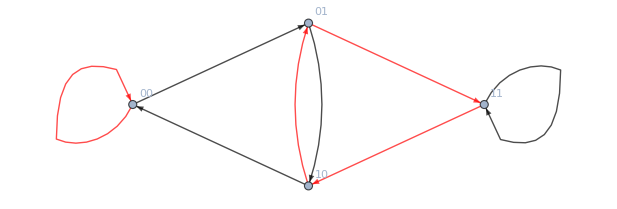

```mathematica
RuleDeBruijnGraph[150,2,1]
```

### Generalisation

#### k = 2, r = 2 (nodes with 4 symbols; overlaps with 3)

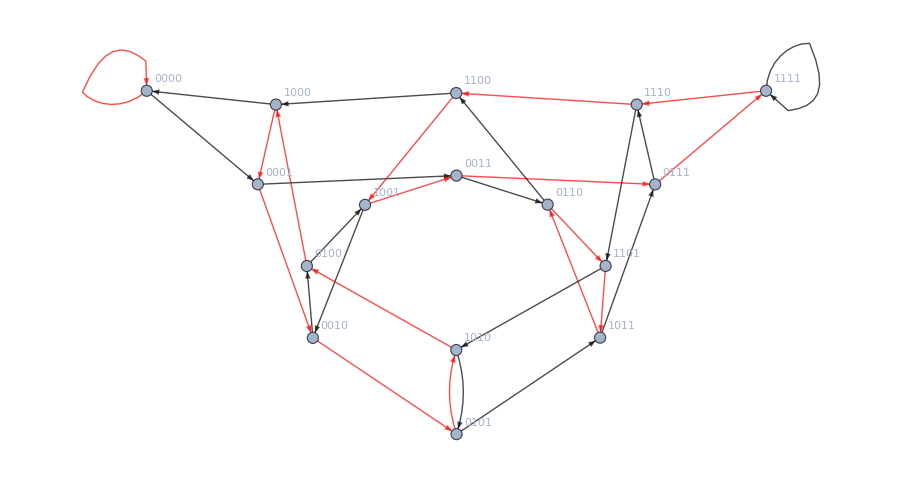

```mathematica
RuleDeBruijnGraph[2779077210,2,2]
```

#### k = 3, r = 1

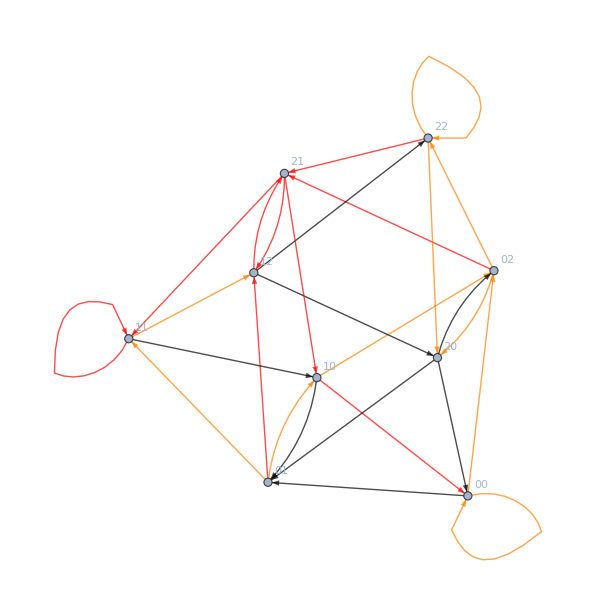

```mathematica
RuleDeBruijnGraph[RandomInteger[{0,3^(3^3)-1}],3,1]
```

#### k = 3, r = 2

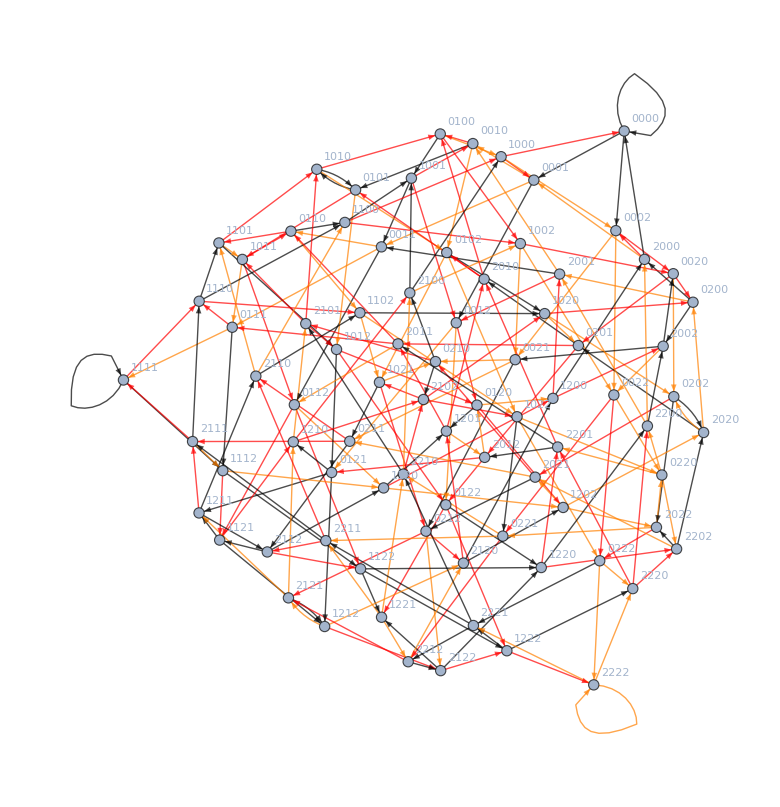

```mathematica
RuleDeBruijnGraph[RandomInteger[{0,3^(3^5)-1}],3,2]
```

### Question 6: Does the block 01010 appear as a path along the edges of the DeBruijn graph of ECA rule 110?

OBS: DeBruijn graphs are useful for various algorithms, such as the determination of the number of preimages of a configuration, and the orphans of a rule. 
Block 01010 is the shortest orphan of rule 110.

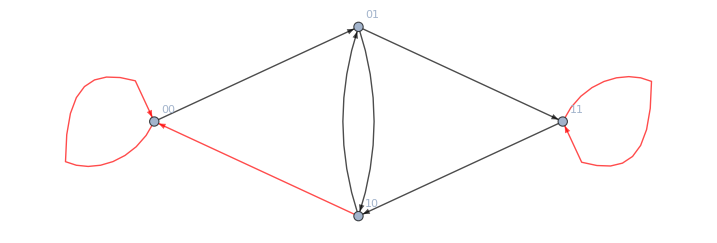

```mathematica
RuleDeBruijnGraph[110,2,1]
```